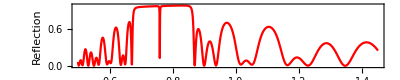

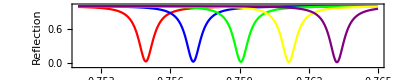

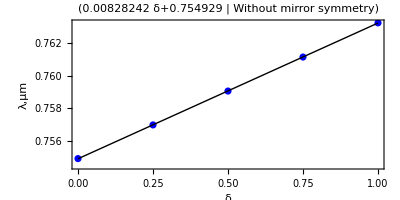

8.28242

```mathematica
Clear["Global`*"];
(*Без зеркальной симметрии(WMS)*)
d1=0.100;
d2=0.114;(*μm*)
Np=8;
(*Кремний-кристаллический, оксид кремния-тонкая пленка, вода и этанол - жидкость*)
Rsi=Import["TiO2.csv"][[1+Range[977]]];
Isi=Import["TiO2.csv"][[980+Range[977]]];
nRsi=Interpolation[Rsi,λ];nIsi=Interpolation[Isi,λ];n1=nRsi+nIsi*I;
rsio2=Import["SIO22.csv"][[1+Range[395]]];
isio2=Import["SIO22.csv"][[398+Range[395]]];
nrsio2=Interpolation[rsio2,λ];
nisio2=Interpolation[isio2,λ];
n2=nrsio2+nisio2*I;
Rh2o=Import["Kedenburg.csv"][[1+Range[101]]];
Ih2o =Import["Kedenburg.csv"][[104+Range[1011]]];
nRh2o=Interpolation[Rh2o,λ];nIh2o=Interpolation[Ih2o,λ];
nd=nRh2o+nIh2o*I;
Ret=Import["Aceton.csv"][[1+Range[101]]];
nRet=Interpolation[Ret,λ];net=nRet;

(*Метод Максвелла Гарнета*)
nddEMA=nd(2*Vet*(net-nd)+net+2nd)/(2*nd+net-Vet(net-nd));
θ=0;
b1=(1/λ)(2Pi*d1)n1*Cos[θ];
b2=(1/λ)(2Pi*d2)n2*Cos[θ];
bdd=((2Pi*dd)/λ)nddEMA*Cos[θ];
p1=n1 *Cos[θ]; 
p2 =n2 *Cos[θ];
pdd=nddEMA*Cos[θ];
L1={{Cos[b1],((-I)/p1)Sin[b1]},{-I*p1*Sin[b1],Cos[b1]}}; L2={{Cos[b2],((-I)/p2)Sin[b2]},{-I*p2*Sin[b2],Cos[b2]}};
Ldd={{Cos[bdd],((-I)/pdd)Sin[bdd]},{-I*pdd*Sin[bdd],Cos[bdd]}};
Q0 = 1;Qf =1;
dd=1;
стили оформления графиков;
labelT = {{"Transmittance",None},{"Wavelength,μm",None}};
labelR = {{"Reflection",None},{"Wavelength,μm",None}};
label = {{"λ,μm",None},{"δ",None}};
style ={FontFamily->"Times New Roman",12,GrayLevel[0]};
color ={Red,Blue,Green,Yellow,Purple};
legend=SwatchLegend[color,{"0","0.25","0.5","0.75","1"} ,LegendMarkers->Graphics[{EdgeForm[Black],Opacity[0.5],Rectangle[]}],LegendLabel->"Concentrations",LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5];
RightWMS=MatrixPower[L2.L1,Np];
LeftWMS=MatrixPower[L2.L1,Np];
Mwms=RightWMS.Ldd.LeftWMS;M11WMS=Mwms[[1,1]];M12WMS=Mwms[[1,2]];M21WMS=Mwms[[2,1]];M22WMS=Mwms[[2,2]];
tWMS=(2*Q0)/((M11WMS+Qf*M12WMS)*Q0+(M21WMS+Qf*M22WMS));
Twms =Abs[tWMS^2];
rWMS=((M11WMS+Qf*M12WMS)*Q0-(M21WMS+Qf*M22WMS))/((M11WMS+Qf*M12WMS)*Q0+(M21WMS+Qf*M22WMS));
Rwms=Abs[rWMS^2];
rl=0.752;ll=0.765;

G1WMS = Plot[Rwms/.{dd->1,Vet->0.5},{λ,0.5,1.45},PlotRange->{-0.01,1},PlotStyle->{{Red}},AspectRatio->2/10,Frame->True,FrameLabel->labelR,LabelStyle->style,PlotPoints->Automatic,ClippingStyle->None]

G2WMS = Plot[{{Rwms/.Vet->0},{Rwms/.Vet->0.25},{Rwms/.Vet->0.5},{Rwms/.Vet->0.75},{Rwms/.Vet->1}},{λ,rl,ll},PlotRange->{-0.05,1.001},PlotStyle->color,AspectRatio->2/10,Frame->True,FrameLabel->labelR,LabelStyle->style ,PlotLegends->legend]

λ1WMS =λ/.Last[FindMinimum[Rwms/.Vet->0,{λ,rl,ll}]];
λ2WMS =λ/.Last[FindMinimum[Rwms/.Vet->0.25,{λ,rl,ll}]];
λ3WMS=λ/.Last[FindMinimum[Rwms/.Vet->0.5,{λ,rl,ll}]];
λ4WMS=λ/.Last[FindMinimum[Rwms/.Vet->0.75,{λ,rl,ll}]];
λ5WMS =λ/.Last[FindMinimum[Rwms/.Vet->1,{λ,0.762,0.764}]];
WMS=List[{0,λ1WMS},{0.25,λ2WMS},{0.5,λ3WMS},{0.75,λ4WMS},{1,λ5WMS}];
G3WMS =ListPlot[{WMS},PlotRange->All,PlotStyle->Blue,AspectRatio->1/2,Frame->True,FrameLabel->label,LabelStyle->style ];
f1 = Fit[WMS, {1,δ},δ];
Show[G3WMS, Plot[f1 , {δ, 0, 1},PlotStyle->Directive[Thin,Black]],PlotLabel->Style[Framed[{{f1,"Without mirror symmetry"}}],16,Black]]
var1=List[{0,Re[n2]/.λ->0.5},{0.05,Re[n2]/.λ->0.5},{0.05,Re[n1]/.λ->0.5},{0.05,Re[n1]/.λ->0.5},{0.075,Re[n1]/.λ->0.5},{0.075,Re[n2]/.λ->0.5}];

f2=D[f1,δ]*1000
```

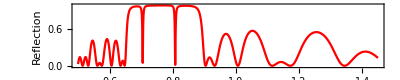

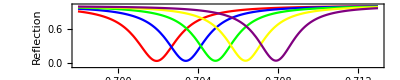

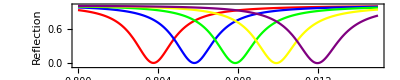

5.96702

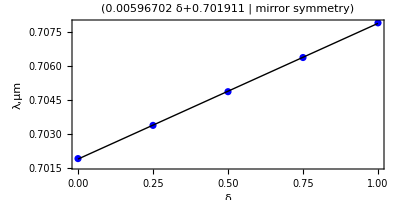

8.19731

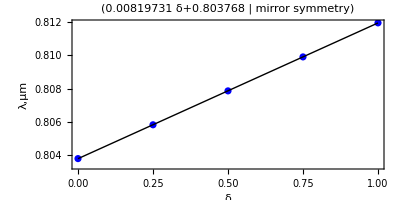

```mathematica
(*Зеркальная симметрия a)(MS)*)
d1=0.100;
d2=0.114;(*μm*)
Np=6;
(*У кремния преломление больше чем у оксида*)
(*Кремний-кристаллический, оксид кремния-тонкая пленка, вода и этанол - жидкость*)
Rsi=Import["TiO2.csv"][[1+Range[977]]];
Isi=Import["TiO2.csv"][[980+Range[977]]];
nRsi=Interpolation[Rsi,λ];nIsi=Interpolation[Isi,λ];n1=nRsi+nIsi*I;
rsio2=Import["SIO22.csv"][[1+Range[395]]];
isio2=Import["SIO22.csv"][[398+Range[395]]];
nrsio2=Interpolation[rsio2,λ];
nisio2=Interpolation[isio2,λ];
n2=nrsio2+nisio2*I;
Rh2o=Import["Kedenburg.csv"][[1+Range[101]]];
Ih2o =Import["Kedenburg.csv"][[104+Range[1011]]];
nRh2o=Interpolation[Rh2o,λ];nIh2o=Interpolation[Ih2o,λ];
nd=nRh2o+nIh2o*I;
Ret=Import["Aceton.csv"][[1+Range[101]]];
nRet=Interpolation[Ret,λ];net=nRet;
(*Метод Максвелла Гарнета*)
nddEMA=nd(2*Vet*(net-nd)+net+2nd)/(2*nd+net-Vet(net-nd));
θ=0;
b1=(1/λ)(2Pi*d1)n1*Cos[θ];
b2=(1/λ)(2Pi*d2)n2*Cos[θ];
bdd=((2Pi*dd)/λ)nddEMA*Cos[θ];
p1=n1 *Cos[θ]; 
p2 =n2 *Cos[θ];
pdd=nddEMA*Cos[θ];
L1={{Cos[b1],((-I)/p1)Sin[b1]},{-I*p1*Sin[b1],Cos[b1]}}; L2={{Cos[b2],((-I)/p2)Sin[b2]},{-I*p2*Sin[b2],Cos[b2]}};
Ldd={{Cos[bdd],((-I)/pdd)Sin[bdd]},{-I*pdd*Sin[bdd],Cos[bdd]}};
Q0 = 1;Qf =1;
dd=1;
стили оформления графиков;
labelT = {{"Transmittance",None},{"Wavelength,μm",None}};
labelR = {{"Reflection",None},{"Wavelength,μm",None}};
label = {{"λ,μm",None},{"δ",None}};
style ={FontFamily->"Times New Roman",12,GrayLevel[0]};
color ={Red,Blue,Green,Yellow,Purple};
legend=SwatchLegend[color,{"0","0.25","0.5","0.75","1"} ,LegendMarkers->Graphics[{EdgeForm[Black],Opacity[0.5],Rectangle[]}],LegendLabel->"Concentrations",LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5];
(*var a*)
RightWMS=MatrixPower[L1.L2,Np];
LeftWMS=MatrixPower[L2.L1,Np];
Mwms=RightWMS.Ldd.LeftWMS;M11WMS=Mwms[[1,1]];M12WMS=Mwms[[1,2]];M21WMS=Mwms[[2,1]];M22WMS=Mwms[[2,2]];
tWMS=(2*Q0)/((M11WMS+Qf*M12WMS)*Q0+(M21WMS+Qf*M22WMS));
Twms =Abs[tWMS^2];
rWMS=((M11WMS+Qf*M12WMS)*Q0-(M21WMS+Qf*M22WMS))/((M11WMS+Qf*M12WMS)*Q0+(M21WMS+Qf*M22WMS));
Rwms=Abs[rWMS^2];
rl=0.698;ll=0.713;
rl1=0.8;ll1=0.815;
G1WMS = Plot[Rwms/.{dd->ddf,Vet->0.5},{λ,0.5,1.45},PlotRange->{-0.01,1},PlotStyle->{{Red}},AspectRatio->2/10,Frame->True,FrameLabel->labelR,LabelStyle->style,PlotPoints->Automatic,ClippingStyle->None]

G2WMS = Plot[{{Rwms/.Vet->0},{Rwms/.Vet->0.25},{Rwms/.Vet->0.5},{Rwms/.Vet->0.75},{Rwms/.Vet->1}},{λ,rl,ll},PlotRange->{-0.05,1.001},PlotStyle->color,AspectRatio->2/10,Frame->True,FrameLabel->labelR,LabelStyle->style ,PlotLegends->legend]
G4WMS = Plot[{{Rwms/.Vet->0},{Rwms/.Vet->0.25},{Rwms/.Vet->0.5},{Rwms/.Vet->0.75},{Rwms/.Vet->1}},{λ,rl1,ll1},PlotRange->{-0.05,1.001},PlotStyle->color,AspectRatio->2/10,Frame->True,FrameLabel->labelR,LabelStyle->style ,PlotLegends->legend]

λ1WMS =λ/.Last[FindMinimum[Rwms/.Vet->0,{λ,rl,ll}]];
λ2WMS =λ/.Last[FindMinimum[Rwms/.Vet->0.25,{λ,rl,ll}]];
λ3WMS=λ/.Last[FindMinimum[Rwms/.Vet->0.5,{λ,rl,ll}]];
λ4WMS=λ/.Last[FindMinimum[Rwms/.Vet->0.75,{λ,rl,ll}]];
λ5WMS =λ/.Last[FindMinimum[Rwms/.Vet->1,{λ,rl,ll}]];
WMS=List[{0,λ1WMS},{0.25,λ2WMS},{0.5,λ3WMS},{0.75,λ4WMS},{1,λ5WMS}];
G3WMS =ListPlot[{WMS},PlotRange->All,PlotStyle->Blue,AspectRatio->1/2,Frame->True,FrameLabel->label,LabelStyle->style ];
f1 = Fit[WMS, {1,δ},δ];
f2=D[f1,δ]*1000
Show[G3WMS, Plot[f1 , {δ, 0, 1},PlotStyle->Directive[Thin,Black]],PlotLabel->Style[Framed[{{f1,"mirror symmetry"}}],16,Black]]

λ11WMS =λ/.Last[FindMinimum[Rwms/.Vet->0,{λ,rl1,ll1}]];
λ22WMS =λ/.Last[FindMinimum[Rwms/.Vet->0.25,{λ,rl1,ll1}]];
λ33WMS=λ/.Last[FindMinimum[Rwms/.Vet->0.5,{λ,rl1,ll1}]];
λ44WMS=λ/.Last[FindMinimum[Rwms/.Vet->0.75,{λ,rl1,ll1}]];
λ55WMS =λ/.Last[FindMinimum[Rwms/.Vet->1,{λ,rl1,ll1}]];
WMS1=List[{0,λ11WMS},{0.25,λ22WMS},{0.5,λ33WMS},{0.75,λ44WMS},{1,λ55WMS}];
G3WMS1 =ListPlot[{WMS1},PlotRange->All,PlotStyle->Blue,AspectRatio->1/2,Frame->True,FrameLabel->label,LabelStyle->style ];
f3 = Fit[WMS1, {1,δ},δ];
f4=D[f3,δ]*1000
Show[G3WMS1, Plot[f3 , {δ, 0, 1},PlotStyle->Directive[Thin,Black]],PlotLabel->Style[Framed[{{f3,"mirror symmetry"}}],16,Black]]
```

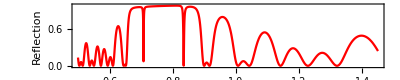

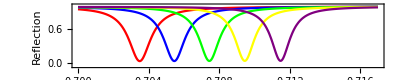

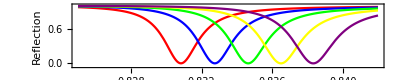

7.98919

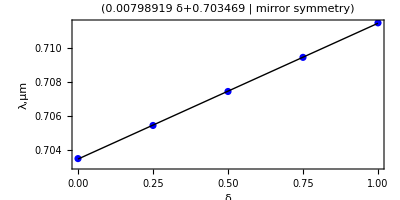

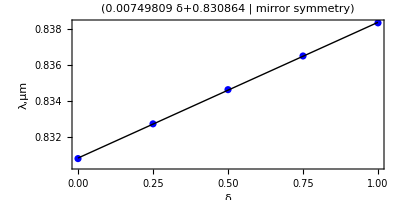

```mathematica
(*Зеркальная симметрия b)(MS)*)
d1=0.100;
d2=0.114;(*μm*)
Np=8;
(*У кремния преломление больше чем у оксида*)
(*Кремний-кристаллический, оксид кремния-тонкая пленка, вода и этанол - жидкость*)
Rsi=Import["TiO2.csv"][[1+Range[977]]];
Isi=Import["TiO2.csv"][[980+Range[977]]];
nRsi=Interpolation[Rsi,λ];nIsi=Interpolation[Isi,λ];n1=nRsi+nIsi*I;
rsio2=Import["SIO22.csv"][[1+Range[395]]];
isio2=Import["SIO22.csv"][[398+Range[395]]];
nrsio2=Interpolation[rsio2,λ];
nisio2=Interpolation[isio2,λ];
n2=nrsio2+nisio2*I;
Rh2o=Import["Kedenburg.csv"][[1+Range[101]]];
Ih2o =Import["Kedenburg.csv"][[104+Range[1011]]];
nRh2o=Interpolation[Rh2o,λ];nIh2o=Interpolation[Ih2o,λ];
nd=nRh2o+nIh2o*I;
Ret=Import["Aceton.csv"][[1+Range[101]]];
nRet=Interpolation[Ret,λ];net=nRet;
(*Метод Максвелла Гарнета*)
nddEMA=nd(2*Vet*(net-nd)+net+2nd)/(2*nd+net-Vet(net-nd));
θ=0;
b1=(1/λ)(2Pi*d1)n1*Cos[θ];
b2=(1/λ)(2Pi*d2)n2*Cos[θ];
bdd=((2Pi*dd)/λ)nddEMA*Cos[θ];
p1=n1 *Cos[θ]; 
p2 =n2 *Cos[θ];
pdd=nddEMA*Cos[θ];
L1={{Cos[b1],((-I)/p1)Sin[b1]},{-I*p1*Sin[b1],Cos[b1]}}; L2={{Cos[b2],((-I)/p2)Sin[b2]},{-I*p2*Sin[b2],Cos[b2]}};
Ldd={{Cos[bdd],((-I)/pdd)Sin[bdd]},{-I*pdd*Sin[bdd],Cos[bdd]}};
Q0 = 1;Qf =1;
dd=1;
стили оформления графиков;
labelT = {{"Transmittance",None},{"Wavelength,μm",None}};
labelR = {{"Reflection",None},{"Wavelength,μm",None}};
label = {{"λ,μm",None},{"δ",None}};
style ={FontFamily->"Times New Roman",12,GrayLevel[0]};
color ={Red,Blue,Green,Yellow,Purple};
legend=SwatchLegend[color,{"0","0.25","0.5","0.75","1"} ,LegendMarkers->Graphics[{EdgeForm[Black],Opacity[0.5],Rectangle[]}],LegendLabel->"Concentrations",LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5];
(*var b*)
RightWMS=MatrixPower[L2.L1,Np];
LeftWMS=MatrixPower[L1.L2,Np];
Mwms=RightWMS.Ldd.LeftWMS;M11WMS=Mwms[[1,1]];M12WMS=Mwms[[1,2]];M21WMS=Mwms[[2,1]];M22WMS=Mwms[[2,2]];
tWMS=(2*Q0)/((M11WMS+Qf*M12WMS)*Q0+(M21WMS+Qf*M22WMS));
Twms =Abs[tWMS^2];
rWMS=((M11WMS+Qf*M12WMS)*Q0-(M21WMS+Qf*M22WMS))/((M11WMS+Qf*M12WMS)*Q0+(M21WMS+Qf*M22WMS));
Rwms=Abs[rWMS^2];
rl=0.7;ll=0.717;
rl1=0.825;ll1=0.842;
G1WMS = Plot[Rwms/.{dd->ddf,Vet->0.5},{λ,0.5,1.45},PlotRange->{-0.01,1},PlotStyle->{{Red}},AspectRatio->2/10,Frame->True,FrameLabel->labelR,LabelStyle->style,PlotPoints->Automatic,ClippingStyle->None]

G2WMS = Plot[{{Rwms/.Vet->0},{Rwms/.Vet->0.25},{Rwms/.Vet->0.5},{Rwms/.Vet->0.75},{Rwms/.Vet->1}},{λ,rl,ll},PlotRange->{-0.05,1.001},PlotStyle->color,AspectRatio->2/10,Frame->True,FrameLabel->labelR,LabelStyle->style ,PlotLegends->legend]
G4WMS = Plot[{{Rwms/.Vet->0},{Rwms/.Vet->0.25},{Rwms/.Vet->0.5},{Rwms/.Vet->0.75},{Rwms/.Vet->1}},{λ,rl1,ll1},PlotRange->{-0.05,1.001},PlotStyle->color,AspectRatio->2/10,Frame->True,FrameLabel->labelR,LabelStyle->style ,PlotLegends->legend]

λ1WMS =λ/.Last[FindMinimum[Rwms/.Vet->0,{λ,rl,ll}]];
λ2WMS =λ/.Last[FindMinimum[Rwms/.Vet->0.25,{λ,rl,ll}]];
λ3WMS=λ/.Last[FindMinimum[Rwms/.Vet->0.5,{λ,rl,ll}]];
λ4WMS=λ/.Last[FindMinimum[Rwms/.Vet->0.75,{λ,rl,ll}]];
λ5WMS =λ/.Last[FindMinimum[Rwms/.Vet->1,{λ,rl,ll}]];
WMS=List[{0,λ1WMS},{0.25,λ2WMS},{0.5,λ3WMS},{0.75,λ4WMS},{1,λ5WMS}];
G3WMS =ListPlot[{WMS},PlotRange->All,PlotStyle->Blue,AspectRatio->1/2,Frame->True,FrameLabel->label,LabelStyle->style ];
f1 = Fit[WMS, {1,δ},δ];
f2=D[f1,δ]*1000
Show[G3WMS, Plot[f1 , {δ, 0, 1},PlotStyle->Directive[Thin,Black]],PlotLabel->Style[Framed[{{f1,"mirror symmetry"}}],16,Black]]

λ11WMS =λ/.Last[FindMinimum[Rwms/.Vet->0,{λ,rl1,ll1}]];
λ22WMS =λ/.Last[FindMinimum[Rwms/.Vet->0.25,{λ,rl1,ll1}]];
λ33WMS=λ/.Last[FindMinimum[Rwms/.Vet->0.5,{λ,rl1,ll1}]];
λ44WMS=λ/.Last[FindMinimum[Rwms/.Vet->0.75,{λ,rl1,ll1}]];
λ55WMS =λ/.Last[FindMinimum[Rwms/.Vet->1,{λ,rl1,ll1}]];
WMS1=List[{0,λ11WMS},{0.25,λ22WMS},{0.5,λ33WMS},{0.75,λ44WMS},{1,λ55WMS}];
G3WMS1 =ListPlot[{WMS1},PlotRange->All,PlotStyle->Blue,AspectRatio->1/2,Frame->True,FrameLabel->label,LabelStyle->style ];
f3 = Fit[WMS1, {1,δ},δ];
f4=D[f3,δ]*1000
Show[G3WMS1, Plot[f3 , {δ, 0, 1},PlotStyle->Directive[Thin,Black]],PlotLabel->Style[Framed[{{f3,"mirror symmetry"}}],16,Black]]
```

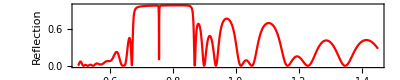

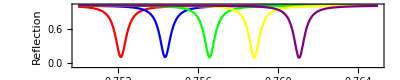

8.913

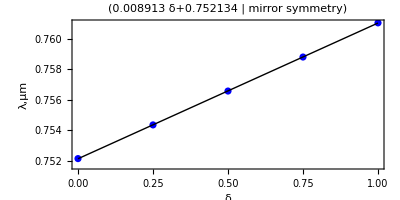

```mathematica
(*Зеркальная симметрия c)(MS)*)
d1=0.1;
d2=0.114/2;(*μm*)
Np=8;
(*У кремния преломление больше чем у оксида*)
(*Кремний-кристаллический, оксид кремния-тонкая пленка, вода и этанол - жидкость*)
Rsi=Import["TiO2.csv"][[1+Range[977]]];
Isi=Import["TiO2.csv"][[980+Range[977]]];
nRsi=Interpolation[Rsi,λ];nIsi=Interpolation[Isi,λ];n1=nRsi+nIsi*I;
rsio2=Import["SIO22.csv"][[1+Range[395]]];
isio2=Import["SIO22.csv"][[398+Range[395]]];
nrsio2=Interpolation[rsio2,λ];
nisio2=Interpolation[isio2,λ];
n2=nrsio2+nisio2*I;
Rh2o=Import["Kedenburg.csv"][[1+Range[101]]];
Ih2o =Import["Kedenburg.csv"][[104+Range[1011]]];
nRh2o=Interpolation[Rh2o,λ];nIh2o=Interpolation[Ih2o,λ];
nd=nRh2o+nIh2o*I;
Ret=Import["Aceton.csv"][[1+Range[101]]];
nRet=Interpolation[Ret,λ];net=nRet;
(*Метод Максвелла Гарнета*)
nddEMA=nd(2*Vet*(net-nd)+net+2nd)/(2*nd+net-Vet(net-nd));
θ=0;
b1=(1/λ)(2Pi*d1)n1*Cos[θ];
b2=(1/λ)(2Pi*d2)n2*Cos[θ];
bdd=((2Pi*dd)/λ)nddEMA*Cos[θ];
p1=n1 *Cos[θ]; 
p2 =n2 *Cos[θ];
pdd=nddEMA*Cos[θ];
L1={{Cos[b1],((-I)/p1)Sin[b1]},{-I*p1*Sin[b1],Cos[b1]}}; L2={{Cos[b2],((-I)/p2)Sin[b2]},{-I*p2*Sin[b2],Cos[b2]}};
Ldd={{Cos[bdd],((-I)/pdd)Sin[bdd]},{-I*pdd*Sin[bdd],Cos[bdd]}};
Q0 = 1;Qf =1;
dd=1;
стили оформления графиков;
labelT = {{"Transmittance",None},{"Wavelength,μm",None}};
labelR = {{"Reflection",None},{"Wavelength,μm",None}};
label = {{"λ,μm",None},{"δ",None}};
style ={FontFamily->"Times New Roman",12,GrayLevel[0]};
color ={Red,Blue,Green,Yellow,Purple};
legend=SwatchLegend[color,{"0","0.25","0.5","0.75","1"} ,LegendMarkers->Graphics[{EdgeForm[Black],Opacity[0.5],Rectangle[]}],LegendLabel->"Concentrations",LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5];
(*var c*)
RightWMS=MatrixPower[L2.L1.L2,Np];
LeftWMS=MatrixPower[L2.L1.L2,Np];
Mwms=RightWMS.Ldd.LeftWMS;M11WMS=Mwms[[1,1]];M12WMS=Mwms[[1,2]];M21WMS=Mwms[[2,1]];M22WMS=Mwms[[2,2]];
tWMS=(2*Q0)/((M11WMS+Qf*M12WMS)*Q0+(M21WMS+Qf*M22WMS));
Twms =Abs[tWMS^2];
rWMS=((M11WMS+Qf*M12WMS)*Q0-(M21WMS+Qf*M22WMS))/((M11WMS+Qf*M12WMS)*Q0+(M21WMS+Qf*M22WMS));
Rwms=Abs[rWMS^2];
rl=0.75;ll=0.765;

G1WMS = Plot[Rwms/.{dd->ddf,Vet->0.5},{λ,0.5,1.45},PlotRange->{-0.01,1},PlotStyle->{{Red}},AspectRatio->2/10,Frame->True,FrameLabel->labelR,LabelStyle->style,PlotPoints->Automatic,ClippingStyle->None]

G2WMS = Plot[{{Rwms/.Vet->0},{Rwms/.Vet->0.25},{Rwms/.Vet->0.5},{Rwms/.Vet->0.75},{Rwms/.Vet->1}},{λ,rl,ll},PlotRange->{-0.05,1.001},PlotStyle->color,AspectRatio->2/10,Frame->True,FrameLabel->labelR,LabelStyle->style ,PlotLegends->legend]

λ1WMS =λ/.Last[FindMinimum[Rwms/.Vet->0,{λ,rl,ll}]];
λ2WMS =λ/.Last[FindMinimum[Rwms/.Vet->0.25,{λ,rl,ll}]];
λ3WMS=λ/.Last[FindMinimum[Rwms/.Vet->0.5,{λ,rl,ll}]];
λ4WMS=λ/.Last[FindMinimum[Rwms/.Vet->0.75,{λ,rl,ll}]];
λ5WMS =λ/.Last[FindMinimum[Rwms/.Vet->1,{λ,0.76,0.762}]];
WMS=List[{0,λ1WMS},{0.25,λ2WMS},{0.5,λ3WMS},{0.75,λ4WMS},{1,λ5WMS}];
G3WMS =ListPlot[{WMS},PlotRange->All,PlotStyle->Blue,AspectRatio->1/2,Frame->True,FrameLabel->label,LabelStyle->style ];
f1 = Fit[WMS, {1,δ},δ];
f2=D[f1,δ]*1000
Show[G3WMS, Plot[f1 , {δ, 0, 1},PlotStyle->Directive[Thin,Black]],PlotLabel->Style[Framed[{{f1,"mirror symmetry"}}],16,Black]]
```

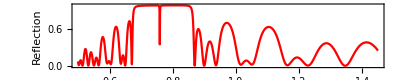

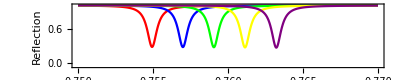

8.2824

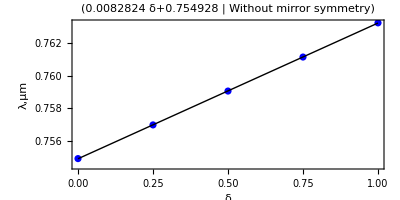

```mathematica
(*Без зеркальной симметрии(WMS)*)
d1=0.100;
d2=0.114;(*μm*)
Np=8;
(*Кремний-кристаллический, оксид кремния-тонкая пленка, вода и этанол - жидкость*)
Rsi=Import["TiO2.csv"][[1+Range[977]]];
Isi=Import["TiO2.csv"][[980+Range[977]]];
nRsi=Interpolation[Rsi,λ];nIsi=Interpolation[Isi,λ];n1=nRsi+nIsi*I;
rsio2=Import["SIO22.csv"][[1+Range[395]]];
isio2=Import["SIO22.csv"][[398+Range[395]]];
nrsio2=Interpolation[rsio2,λ];
nisio2=Interpolation[isio2,λ];
n2=nrsio2+nisio2*I;
Rh2o=Import["Kedenburg.csv"][[1+Range[101]]];
Ih2o =Import["Kedenburg.csv"][[104+Range[1011]]];
nRh2o=Interpolation[Rh2o,λ];nIh2o=Interpolation[Ih2o,λ];
nd=nRh2o+nIh2o*I;
Ret=Import["Aceton.csv"][[1+Range[101]]];
nRet=Interpolation[Ret,λ];net=nRet;
(*Метод Максвелла Гарнета*)
nddEMA=nd(2*Vet*(net-nd)+net+2nd)/(2*nd+net-Vet(net-nd));
θ=0;
b1=(1/λ)(2Pi*d1)n1*Cos[θ];
b2=(1/λ)(2Pi*d2)n2*Cos[θ];
bdd=((2Pi*dd)/λ)nddEMA*Cos[θ];
p1=n1 *Cos[θ]; 
p2 =n2 *Cos[θ];
pdd=nddEMA*Cos[θ];
L1={{Cos[b1],((-I)/p1)Sin[b1]},{-I*p1*Sin[b1],Cos[b1]}}; L2={{Cos[b2],((-I)/p2)Sin[b2]},{-I*p2*Sin[b2],Cos[b2]}};
Ldd={{Cos[bdd],((-I)/pdd)Sin[bdd]},{-I*pdd*Sin[bdd],Cos[bdd]}};
Q0 = 1;Qf =1;
dd=1;
стили оформления графиков;
labelT = {{"Transmittance",None},{"Wavelength,μm",None}};
labelR = {{"Reflection",None},{"Wavelength,μm",None}};
label = {{"λ,μm",None},{"δ",None}};
style ={FontFamily->"Times New Roman",12,GrayLevel[0]};
color ={Red,Blue,Green,Yellow,Purple};
legend=SwatchLegend[color,{"0","0.25","0.5","0.75","1"} ,LegendMarkers->Graphics[{EdgeForm[Black],Opacity[0.5],Rectangle[]}],LegendLabel->"Concentrations",LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5];

RightWMS=MatrixPower[L1.L2,Np];
LeftWMS=MatrixPower[L1.L2,Np];
Mwms=RightWMS.Ldd.LeftWMS;M11WMS=Mwms[[1,1]];M12WMS=Mwms[[1,2]];M21WMS=Mwms[[2,1]];M22WMS=Mwms[[2,2]];
tWMS=(2*Q0)/((M11WMS+Qf*M12WMS)*Q0+(M21WMS+Qf*M22WMS));
Twms =Abs[tWMS^2];
rWMS=((M11WMS+Qf*M12WMS)*Q0-(M21WMS+Qf*M22WMS))/((M11WMS+Qf*M12WMS)*Q0+(M21WMS+Qf*M22WMS));
Rwms=Abs[rWMS^2];
rl=0.75;ll=0.77;
G1WMS = Plot[Rwms/.{dd->ddf,Vet->0.5},{λ,0.5,1.45},PlotRange->{-0.01,1},PlotStyle->{{Red}},AspectRatio->2/10,Frame->True,FrameLabel->labelR,LabelStyle->style,PlotPoints->Automatic,ClippingStyle->None]

G2WMS = Plot[{{Rwms/.Vet->0},{Rwms/.Vet->0.25},{Rwms/.Vet->0.5},{Rwms/.Vet->0.75},{Rwms/.Vet->1}},{λ,rl,ll},PlotRange->{-0.05,1.001},PlotStyle->color,AspectRatio->2/10,Frame->True,FrameLabel->labelR,LabelStyle->style ,PlotLegends->legend]

λ1WMS =λ/.Last[FindMinimum[Rwms/.Vet->0,{λ,rl,ll}]];
λ2WMS =λ/.Last[FindMinimum[Rwms/.Vet->0.25,{λ,rl,ll}]];
λ3WMS=λ/.Last[FindMinimum[Rwms/.Vet->0.5,{λ,rl,ll}]];
λ4WMS=λ/.Last[FindMinimum[Rwms/.Vet->0.75,{λ,rl,ll}]];
λ5WMS =λ/.Last[FindMinimum[Rwms/.Vet->1,{λ,rl,ll}]];
WMS=List[{0,λ1WMS},{0.25,λ2WMS},{0.5,λ3WMS},{0.75,λ4WMS},{1,λ5WMS}];
G3WMS =ListPlot[{WMS},PlotRange->All,PlotStyle->Blue,AspectRatio->1/2,Frame->True,FrameLabel->label,LabelStyle->style ];
f1 = Fit[WMS, {1,δ},δ];
f2=D[f1,δ]*1000
Show[G3WMS, Plot[f1 , {δ, 0, 1},PlotStyle->Directive[Thin,Black]],PlotLabel->Style[Framed[{{f1,"Without mirror symmetry"}}],16,Black]]
```

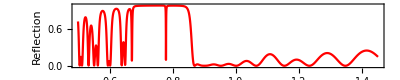

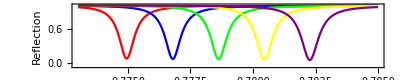

7.32644

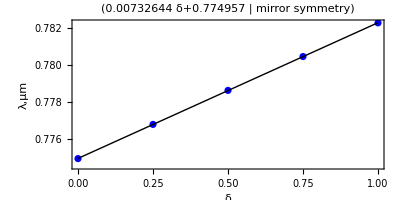

```mathematica
(*Зеркальная симметрия d)(MS)*)
d1=0.1/2;
d2=0.114;(*μm*)
Np=8;
(*У кремния преломление больше чем у оксида*)
(*Кремний-кристаллический, оксид кремния-тонкая пленка, вода и этанол - жидкость*)
Rsi=Import["TiO2.csv"][[1+Range[977]]];
Isi=Import["TiO2.csv"][[980+Range[977]]];
nRsi=Interpolation[Rsi,λ];nIsi=Interpolation[Isi,λ];n1=nRsi+nIsi*I;
rsio2=Import["SIO22.csv"][[1+Range[395]]];
isio2=Import["SIO22.csv"][[398+Range[395]]];
nrsio2=Interpolation[rsio2,λ];
nisio2=Interpolation[isio2,λ];
n2=nrsio2+nisio2*I;
Rh2o=Import["Kedenburg.csv"][[1+Range[101]]];
Ih2o =Import["Kedenburg.csv"][[104+Range[1011]]];
nRh2o=Interpolation[Rh2o,λ];nIh2o=Interpolation[Ih2o,λ];
nd=nRh2o+nIh2o*I;
Ret=Import["Aceton.csv"][[1+Range[101]]];
nRet=Interpolation[Ret,λ];net=nRet;
(*Метод Максвелла Гарнета*)
nddEMA=nd(2*Vet*(net-nd)+net+2nd)/(2*nd+net-Vet(net-nd));
θ=0;
b1=(1/λ)(2Pi*d1)n1*Cos[θ];
b2=(1/λ)(2Pi*d2)n2*Cos[θ];
bdd=((2Pi*dd)/λ)nddEMA*Cos[θ];
p1=n1 *Cos[θ]; 
p2 =n2 *Cos[θ];
pdd=nddEMA*Cos[θ];
L1={{Cos[b1],((-I)/p1)Sin[b1]},{-I*p1*Sin[b1],Cos[b1]}}; L2={{Cos[b2],((-I)/p2)Sin[b2]},{-I*p2*Sin[b2],Cos[b2]}};
Ldd={{Cos[bdd],((-I)/pdd)Sin[bdd]},{-I*pdd*Sin[bdd],Cos[bdd]}};
Q0 = 1;Qf =1;
dd=1;
стили оформления графиков;
labelT = {{"Transmittance",None},{"Wavelength,μm",None}};
labelR = {{"Reflection",None},{"Wavelength,μm",None}};
label = {{"λ,μm",None},{"δ",None}};
style ={FontFamily->"Times New Roman",12,GrayLevel[0]};
color ={Red,Blue,Green,Yellow,Purple};
legend=SwatchLegend[color,{"0","0.25","0.5","0.75","1"} ,LegendMarkers->Graphics[{EdgeForm[Black],Opacity[0.5],Rectangle[]}],LegendLabel->"Concentrations",LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5];
(*var d*)
RightWMS=MatrixPower[L1.L2.L1,Np];
LeftWMS=MatrixPower[L1.L2.L1,Np];
Mwms=RightWMS.Ldd.LeftWMS;M11WMS=Mwms[[1,1]];M12WMS=Mwms[[1,2]];M21WMS=Mwms[[2,1]];M22WMS=Mwms[[2,2]];
tWMS=(2*Q0)/((M11WMS+Qf*M12WMS)*Q0+(M21WMS+Qf*M22WMS));
Twms =Abs[tWMS^2];
rWMS=((M11WMS+Qf*M12WMS)*Q0-(M21WMS+Qf*M22WMS))/((M11WMS+Qf*M12WMS)*Q0+(M21WMS+Qf*M22WMS));
Rwms=Abs[rWMS^2];
rl=0.773;ll=0.785;(*  1.155 1.17rl=0.875;ll=0.895;*)

G1WMS = Plot[Rwms/.{dd->ddf,Vet->0.5},{λ,0.5,1.45},PlotRange->{-0.01,1},PlotStyle->{{Red}},AspectRatio->2/10,Frame->True,FrameLabel->labelR,LabelStyle->style,PlotPoints->Automatic,ClippingStyle->None]

G2WMS = Plot[{{Rwms/.Vet->0},{Rwms/.Vet->0.25},{Rwms/.Vet->0.5},{Rwms/.Vet->0.75},{Rwms/.Vet->1}},{λ,rl,ll},PlotRange->{-0.05,1.001},PlotStyle->color,AspectRatio->2/10,Frame->True,FrameLabel->labelR,LabelStyle->style ,PlotLegends->legend]

λ1WMS =λ/.Last[FindMinimum[Rwms/.Vet->0,{λ,rl,ll}]];
λ2WMS =λ/.Last[FindMinimum[Rwms/.Vet->0.25,{λ,0.774,0.7755}]];
λ3WMS=λ/.Last[FindMinimum[Rwms/.Vet->0.5,{λ,0.776,0.7775}]];
λ4WMS=λ/.Last[FindMinimum[Rwms/.Vet->0.75,{λ,0.778,0.7781}]];
λ5WMS =λ/.Last[FindMinimum[Rwms/.Vet->1,{λ,0.77815,0.783}]];
WMS=List[{0,λ1WMS},{0.25,λ2WMS},{0.5,λ3WMS},{0.75,λ4WMS},{1,λ5WMS}];
G3WMS =ListPlot[{WMS},PlotRange->All,PlotStyle->Blue,AspectRatio->1/2,Frame->True,FrameLabel->label,LabelStyle->style ];
f1 = Fit[WMS, {1,δ},δ];
f2=D[f1,δ]*1000
Show[G3WMS, Plot[f1 , {δ, 0, 1},PlotStyle->Directive[Thin,Black]],PlotLabel->Style[Framed[{{f1,"mirror symmetry"}}],16,Black]]
```

```mathematica
n1/.λ->1
n2/.λ->1
```

2.07566+0. ⅈ

1.45911+0.00104104 ⅈ

1.45911+0.00104104 ⅈ